```mathematica
X[J_,μ_]:=1/2(J+μ);
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+Exp[-J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+Exp[-J]));
```

```mathematica
ξ[J_,μ_] := Log[λp[J,μ]/λm[J,μ]]^-1;
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
Z[J_,μ_,Nm_]:= λp[J,μ]^Nm + λm[J,μ]^Nm;
```

```mathematica
Φ[J_,μ_,Nm_]:= 1/2(1 + Tanh[Nm/(2ξ[J,μ])] Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) );
Φ2[J_,μ_,Nm_]:= 1/4(1 + Sinh[X[J,μ]]^2/(Sinh[X[J,μ]]^2+Exp[-J])+Tanh[Nm/(2ξ[J,μ])]((2Sinh[X[J,μ]])/(√(Sinh[X[J,μ]]^2+Exp[-J]))+1/Nm (Exp[-J]Cosh[X[J,μ]])/((Sinh[X[J,μ]]^2+Exp[-J])^(3/2))));
```

```mathematica
Φm[J_,μ_,Nm_]:= 1/Z[J,μ,Nm] 1/(1+vm[J,μ]^2)(λp[J,μ]^Nm + λm[J,μ]^Nm vm[J,μ]^2);
Φm2[J_,μ_,Nm_]:=  1/(Z[J,μ,Nm]Nm)1/((1+vm[J,μ]^2)^2)(λp[J,μ]^Nm ((vm[J,μ]^2 Exp[(1-Nm)/ξ[J,μ]](Exp[Nm/ξ[J,μ]]-1))/(Exp[1/ξ[J,μ]] - 1)+Nm)+ λm[J,μ]^Nm vm[J,μ]^2((vm[J,μ]^2 Exp[1/ξ[J,μ]]Nm - vm[J,μ]^2 Nm + Exp[Nm/ξ [J,μ]]-1)/(Exp[1/ξ[J,μ]]-1)));
```

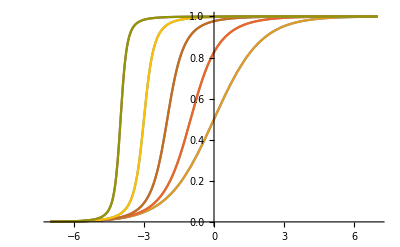

```mathematica
Plot[Evaluate[Table[{Φ[J,μ,13],Φm[J,μ,13]},{J,0.0000000001,5}]],{μ,-7,7}]
```

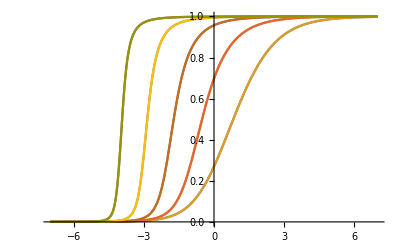

```mathematica
Plot[Evaluate[Table[{Φ2[J,μ,13],Φm2[J,μ,13]},{J,0.0000000001,5}]],{μ,-7,7}]
```

```mathematica
Φ2[0.00000001,0,13]==Φm2[0.00000001,0,13]
```

True